```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/github/neuphysics/codebase/mma/dispersion-relation

```mathematica
Get["../../neupackage/mma/dispersion-relation.wl"]
```

```mathematica
pltcolors=ColorData[97,"ColorList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
colorf=Blend[{Blue,Red},#]&;
colorRainbow=ColorData["Rainbow"];
colorTemp=ColorData["Temperature"];
plotLegend[{min_,max_},n_,col_]:=Graphics[{{col[(#-1)/(n-1)],Rectangle[{0,#-1},{1,#}]},{Black,Text[NumberForm[Rescale[#,{1,n},{min,max}],{4,2}],{3,#-.5},{1,0}]}}&/@Range@n,Frame->True,FrameTicks->None,PlotRangePadding->.5]
```

## Define Beams

```mathematica
NBeamsLR[4]
```

{{-π/2,0.451027},{-π/2,0.795399},{π/2,1.0472},{π/2,1.2661}}

```mathematica
spectDBWC1={{1,-0.6},{1,0.6}}
spectDBWC2={{0.5,-0.6},{1,0.6}}
spectDBWC3={{0.1,-0.6},{1,0.6}}
```

{{1,-0.6},{1,0.6}}

{{0.5,-0.6},{1,0.6}}

{{0.1,-0.6},{1,0.6}}

```mathematica
spectDBC1={{-1,-0.6},{1,0.6}}
spectDBC2={{-0.5,-0.6},{1,0.6}}
spectDBC3={{-0.1,-0.6},{1,0.6}}
```

{{-1,-0.6},{1,0.6}}

{{-0.5,-0.6},{1,0.6}}

{{-0.1,-0.6},{1,0.6}}

## Define Useful Functions

```mathematica
DBPltDRMAA[spect_,pltRange_:{{-2,2},{-2,2}}]:=Module[{spectM},

spectM=spect;

ParametricPlot[
{DBAxialSymKNMAA[spectM, n],DBAxialSymOmegaNMAA[spectM, n]},
{n,-50,50},
PlotRange->pltRange,
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"DR for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"}
]
]
```

```mathematica
DBPltDRMZA[spect_,pltRange_:{{-2,2},{-2,2}}]:=Module[{spectM},

spectM=spect;

ParametricPlot[
Evaluate[
{n #, #} &/@DBAxialSymOmegaNMZA[spectM, n]
],
{n,-50,50},
PlotRange->pltRange,
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"DR for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"},PlotLegends->{"MZA+","MZA-"}
]
]
```

```mathematica
DBPltOmegaN[spect_,range_:{{-10,10},{-1,1}}]:=Module[{spectM},

spectM=spect;

Plot[
DBAxialSymOmegaNMAA[spectM, n],
{n,range[[1,1]],range[[1,2]]},
PlotRange->range,
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"ω(n) for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"}
]
]
```

```mathematica
DBPltKN[spect_,range_:{{-10,10},{-1,1}}]:=Module[{spectM},

spectM=spect;

Plot[
DBAxialSymKNMAA[spectM, n],
{n,range[[1,1]],range[[1,2]]},
PlotRange->range,
Exclusions->((n #[[2]]==1)&/@spectM),ExclusionsStyle->Directive[Dashed,LightGray],
PlotTheme->"Scientific",Frame->True,ImageSize->Large,PlotLabel->"k(n) for spectrum "<>ToString[spectM],FrameLabel->{"k","ω"}
]
]
```

```mathematica
pltDROmegaRealLSA[data_,drplot_]:=Show[
Graphics[
{Point[{#[[2]],#[[1]]}&/@data,VertexColors->colorf/@Rescale@(Abs@#[[3]]&/@data)],Inset[plotLegend[{Min@#,Max@#}&@(Abs@#[[3]]&/@data),20,colorf],Scaled[{1,1/2}],ImageScaled[{-0.1,1/2}],Scaled[{1/4,0.9}]]
},Axes->True,Frame->True,ImageSize->Large,FrameLabel->{"k.real","omega.real"},
ImageSize->Large,
ImagePadding->{{20, 90}, {20, 20}},
AspectRatio->1,PlotRange->{{-4.5,4.5},{-4.5,4.5}}
],
drplot
]
```

## Calculate DR

Plots

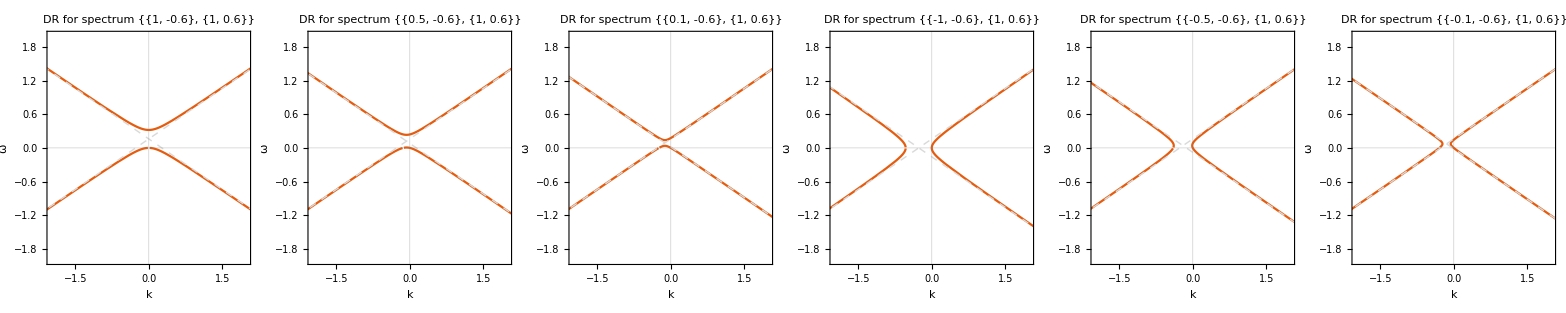

```mathematica
Grid@{
{pltDRMAADBWC1,pltDRMAADBWC2,pltDRMAADBWC3,pltDRMAADBC1,pltDRMAADBC2,pltDRMAADBC3}=Table[
DBPltDRMAA[spectra,{{-2,2},{-2,2}}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
]
}
```

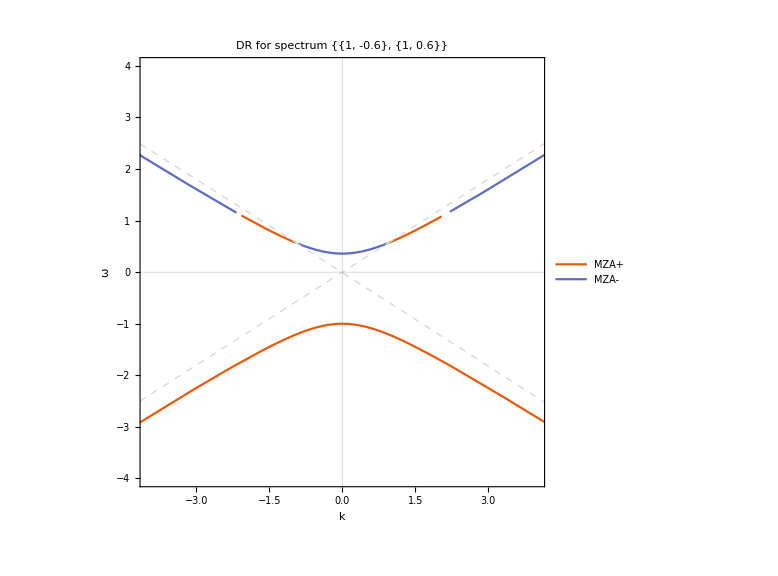
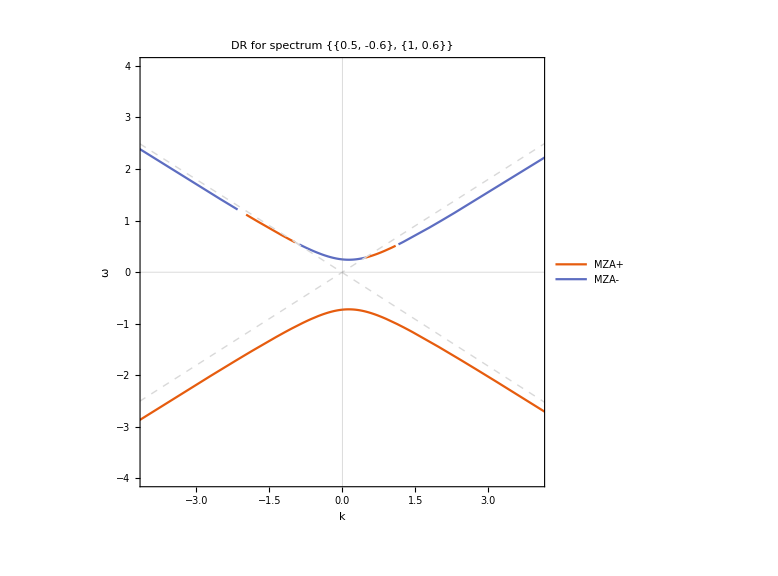
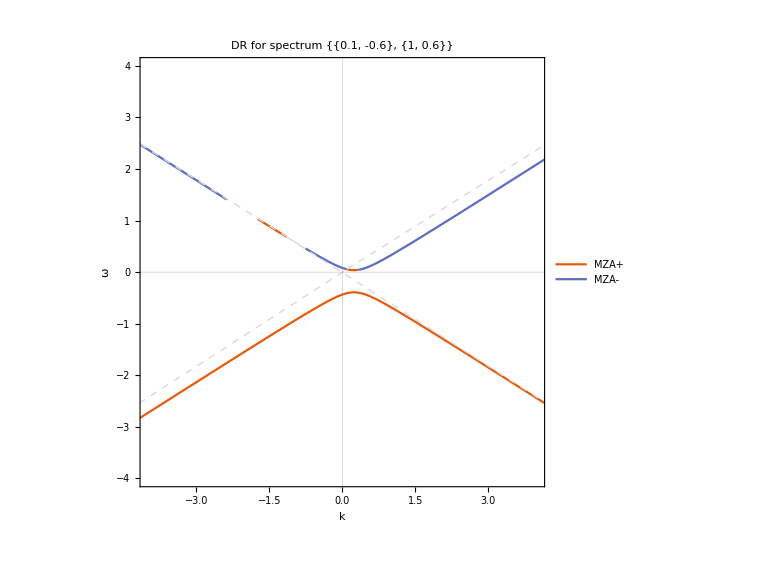
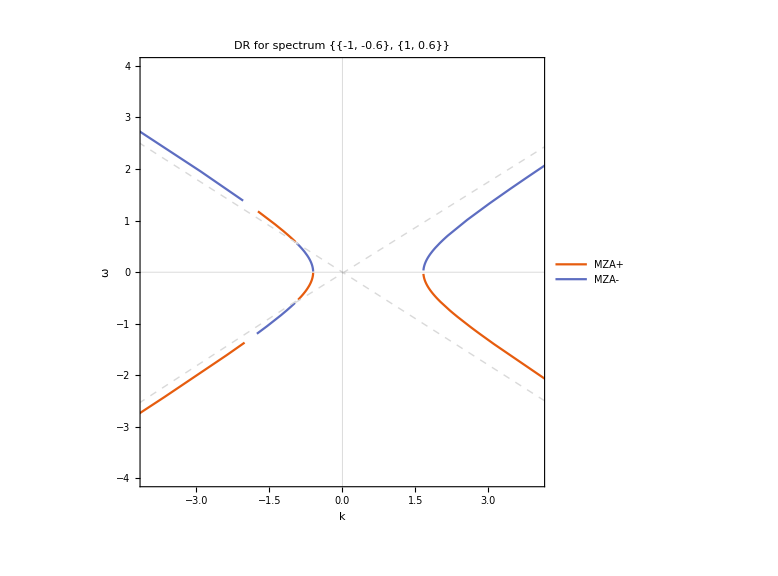
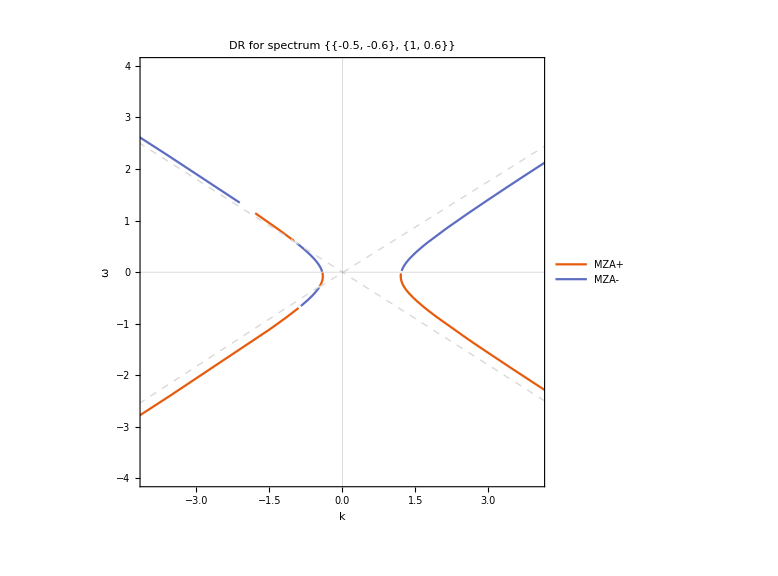
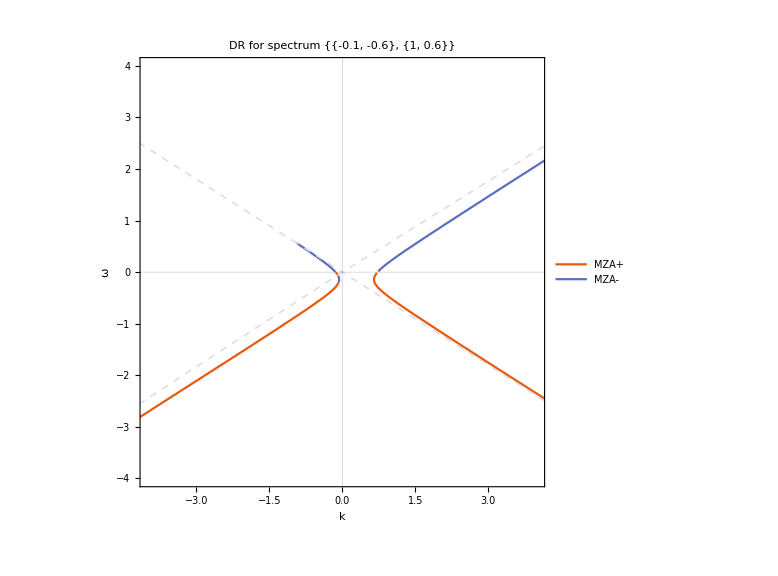
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid@{
{pltDRMZADBWC1,pltDRMZADBWC2,pltDRMZADBWC3,pltDRMZADBC1,pltDRMZADBC2,pltDRMZADBC3}=Table[
DBPltDRMZA[spectra,{{-4,4},{-4,4}}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
]
}
```

## Calculate Instability

Real Omega MAA

```mathematica
{lsaMAARODataRawDBWC1,lsaMAARODataRawDBWC2,lsaMAARODataRawDBWC3,lsaMAARODataRawDBC1,lsaMAARODataRawDBC2,lsaMAARODataRawDBC3} = Table[
LSAMAARODataRawDB[spectra,{-4,4,0.1}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
];
```

```mathematica
Table[
Symbol["lsaMAARODataDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMAARODataDBWC1,lsaMAARODataDBWC2,lsaMAARODataDBWC3,lsaMAARODataDBC1,lsaMAARODataDBC2,lsaMAARODataDBC3}

```mathematica
lsaMAARODataDBList=Table[
LSAMAARODataDB[Symbol["lsaMAARODataRawDB"<>spectraid],Symbol["spectDB"<>spectraid] ],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
{lsaMAARODataDBWC1,lsaMAARODataDBWC2,lsaMAARODataDBWC3,lsaMAARODataDBC1,lsaMAARODataDBC2,lsaMAARODataDBC3}=lsaMAARODataDBList;
```

```mathematica
lsaMAAROPltDBList=Table[
pltDROmegaRealLSA[
Symbol["lsaMAARODataDB"<>spectraid],Symbol["pltDRMAADB"<>spectraid] 
],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
Grid@{lsaMAAROPltDBList}
```

-Graphics-

Real Omega MZAp

Generate the variable names

```mathematica
Table[
Symbol["lsaMZApRODataRawDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMZApRODataRawDBWC1,lsaMZApRODataRawDBWC2,lsaMZApRODataRawDBWC3,lsaMZApRODataRawDBC1,lsaMZApRODataRawDBC2,lsaMZApRODataRawDBC3}

```mathematica
Table[
Symbol["lsaMZApRODataDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMZApRODataDBWC1,lsaMZApRODataDBWC2,lsaMZApRODataDBWC3,lsaMZApRODataDBC1,lsaMZApRODataDBC2,lsaMZApRODataDBC3}

Calculate the instabilities

```mathematica
{lsaMZApRODataRawDBWC1,lsaMZApRODataRawDBWC2,lsaMZApRODataRawDBWC3,lsaMZApRODataRawDBC1,lsaMZApRODataRawDBC2,lsaMZApRODataRawDBC3}= Table[
LSAMZApRODataRawDB[spectra,{-4,4,0.1}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
];
```

```mathematica
lsaMZApRODataDBList=Table[
LSAMZApRODataDB[Symbol["lsaMZApRODataRawDB"<>spectraid],Symbol["spectDB"<>spectraid] ],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
{lsaMZApRODataDBWC1,lsaMZApRODataDBWC2,lsaMZApRODataDBWC3,lsaMZApRODataDBC1,lsaMZApRODataDBC2,lsaMZApRODataDBC3}=lsaMZApRODataDBList;
```

```mathematica
lsaMZApROPltDBList=Table[
pltDROmegaRealLSA[
Symbol["lsaMZApRODataDB"<>spectraid],Symbol["pltDRMZADB"<>spectraid] 
],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
Grid@{lsaMZApROPltDBList}
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Real Omega MZAm

Generate the variable names

```mathematica
Table[
Symbol["lsaMZAmRODataRawDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMZAmRODataRawDBWC1,lsaMZAmRODataRawDBWC2,lsaMZAmRODataRawDBWC3,lsaMZAmRODataRawDBC1,lsaMZAmRODataRawDBC2,lsaMZAmRODataRawDBC3}

```mathematica
Table[
Symbol["lsaMZAmRODataDB"<>spectraid],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
]
```

{lsaMZAmRODataDBWC1,lsaMZAmRODataDBWC2,lsaMZAmRODataDBWC3,lsaMZAmRODataDBC1,lsaMZAmRODataDBC2,lsaMZAmRODataDBC3}

Calculate the instabilities

```mathematica
{lsaMZAmRODataRawDBWC1,lsaMZAmRODataRawDBWC2,lsaMZAmRODataRawDBWC3,lsaMZAmRODataRawDBC1,lsaMZAmRODataRawDBC2,lsaMZAmRODataRawDBC3}= Table[
LSAMZAmRODataRawDB[spectra,{-4,4,0.1}],
{spectra,{spectDBWC1,spectDBWC2,spectDBWC3,spectDBC1,spectDBC2,spectDBC3}}
];
```

```mathematica
lsaMZAmRODataDBList=Table[
LSAMZAmRODataDB[Symbol["lsaMZAmRODataRawDB"<>spectraid],Symbol["spectDB"<>spectraid] ],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
```

```mathematica
{lsaMZAmRODataDBWC1,lsaMZAmRODataDBWC2,lsaMZAmRODataDBWC3,lsaMZAmRODataDBC1,lsaMZAmRODataDBC2,lsaMZAmRODataDBC3}=lsaMZAmRODataDBList;
```

```mathematica
lsaMZAmROPltDBList=Table[
pltDROmegaRealLSA[
Symbol["lsaMZAmRODataDB"<>spectraid],Symbol["pltDRMZADB"<>spectraid] 
],
{spectraid,{"WC1","WC2","WC3","C1","C2","C3"}}
];
Grid@{lsaMZAmROPltDBList}
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

Real k MAA

Real k MZA